```mathematica
(*取100个离散样本点的无限深势阱数值求解，边界条件：0和101处都为0*)
```

```mathematica
h= Table[If[i==j,2,0],{i,1,100},{j,0,100}];
```

```mathematica
k= Table[If[j==i-1,-1,0],{i,1,100},{j,1,100}];
l= Table[If[j==i+1,-1,0],{i,1,100},{j,1,100}];
H=Table[h[[i,j]]+k[[i,j]]+l[[i,j]],{i,1,100},{j,1,100}];
```

```mathematica
EIG=Eigenvalues[N[H]];
```

```mathematica
101^2/π^2*EIG;
```

```mathematica
EVE=Eigenvectors[N[H]];
```

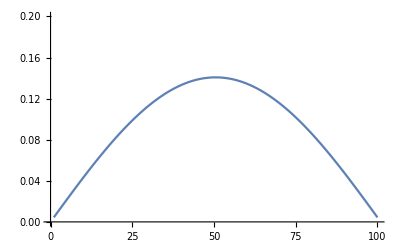

```mathematica
ListLinePlot[EVE[[100]],PlotRange->{0,0.2}]
```

```mathematica
(*此处无限深势阱a=100，则 √(2/a)=0.1414213562373095*)
```